## Comparison of Fourier Cosine and Sine Series for F(x)=x defined on 0<x<L.

### Fourier Cosine Series

#### Define the even function on -L<x<L and its periodic extension. Plot the function. Mod[x, 2*L, -L] =Remaider((x+L)/(2L))-L, so it maps x back into the range -L<x<L.

```mathematica
Clear[L]; fevenbas[x_]:=If[x>0,x,-x]
feven[x_]:=fevenbas[Mod[x,2*L,-L]]
```

```mathematica
PSCos[x_,nMax_]:=L/2+(2L)/π^2∑_(n=1)^nMax ((-1)^n-1)/n^2 Cos[(n*π*x)/L]
FCScoefs=Table[{n,If[n==0,L/2,(2L((-1)^n-1))/(π^2 n^2)]},{n,0,10}];Style[TableForm[FCScoefs,TableHeadings->{None,{"n","A_n"}},TableAlignments->Center],12]
```

n | A_n
0 | L/2
1 | -(4 L)/π^2
2 | 0
3 | -(4 L)/(9 π^2)
4 | 0
5 | -(4 L)/(25 π^2)
6 | 0
7 | -(4 L)/(49 π^2)
8 | 0
9 | -(4 L)/(81 π^2)
10 | 0

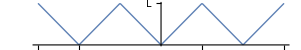

```mathematica
L=1;Plot[feven[x],{x,-3L,3L},BaseStyle->{FontSize->18},PlotStyle->Thick,Ticks-> {{{-3,"-3L"},{-2,"-2L"},{-2,"-2L"},{-1,"-L"},{1,"L"},{2,"2L"},{3,"3L"}},{{1,"L"}}},AspectRatio->1/6]
```

#### Fourier Cosine Series has no jump discontinuities so converges uniformly. The first derivative has jump discontinuities so the Fourier Cosine Series converges as 1/n^2.

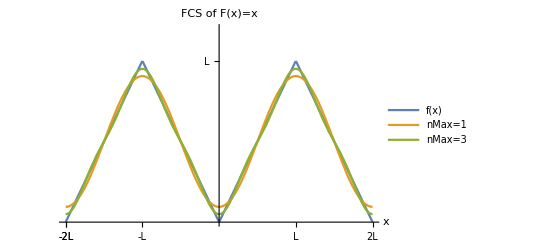

```mathematica
Plot[{feven[x],PSCos[x,1],PSCos[x,3]},{x,-2L,2L},PlotLabel->"FCS of F(x)=x", AxesLabel->{"x",""},PlotRange->{0,1.2},BaseStyle->{FontSize->18},PlotStyle->Thick,PlotLegends->{"f(x)","nMax=1","nMax=3"},Ticks-> {{{-2,"-2L"},{-2,"-2L"},{-1,"-L"},{1,"L"},{2,"2L"}},{{1,"L"}}}]
```

#### Error of Fourier Cosine Series to show ~1% error for 10 terms.

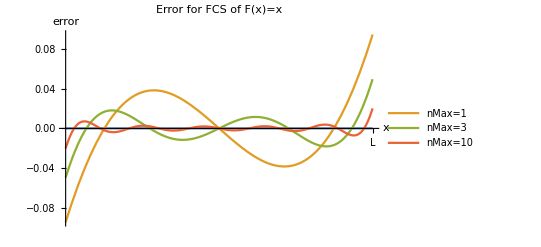

```mathematica
Plot[{0,feven[x]-PSCos[x,1],feven[x]-PSCos[x,3],feven[x]-PSCos[x,10]},{x,0,L},PlotLabel->"Error for FCS of F(x)=x", AxesLabel->{"x","error"},PlotRange->All,BaseStyle->{FontSize->18},PlotStyle->Thick,PlotLegends->{"","nMax=1","nMax=3","nMax=10"},Ticks-> {{{1,"L"}},Automatic}]
```

```mathematica
Animate[Plot[{feven[x],PSCos[x,nMax]},{x,-L,L},PlotRange->{0,1.},PlotLabel->Row[{"nMax = ",PaddedForm[nMax,{4,0}]}],AxesLabel->{"x","FCS"},BaseStyle->{FontSize->18},PlotStyle->Thick,Ticks-> {{{-1,"-L"},{1,"L"}},{{1,"L"}}}],{nMax,0,20,1},AnimationRunning->False]
```

### Fourier Sine Series

#### Define the odd function on -L<x<L and its periodic extension.

```mathematica
Clear[L];foddbas[x_]:=If[x>0,x,x]
fodd[x_]:=foddbas[Mod[x,2*L,-L]]
```

```mathematica
PSSin[x_,nMax_]:=(2L)/π∑_(n=1)^nMax (-1)^(n+1)/n Sin[(n*π*x)/L]
FSScoefs=Table[{n,(2L)/(π n)(-1)^(n+1)},{n,1,10}];Style[TableForm[FSScoefs,TableHeadings->{None,{"n","B_n"}},TableAlignments->Center],14]
```

n | B_n
1 | (2 L)/π
2 | -L/π
3 | (2 L)/(3 π)
4 | -L/(2 π)
5 | (2 L)/(5 π)
6 | -L/(3 π)
7 | (2 L)/(7 π)
8 | -L/(4 π)
9 | (2 L)/(9 π)
10 | -L/(5 π)

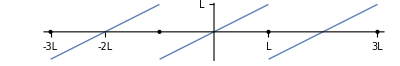

```mathematica
L=1;Plot[fodd[x],{x,-3L,3L},BaseStyle->{FontSize->18},PlotStyle->Thick,Ticks-> {{{-3,"-3L"},{-2,"-2L"},{-2,"-2L"},{-1,"-L"},{1,"L"},{2,"2L"},{3,"3L"}},{{1,"L"}}},Exclusions->{x==-L,x==L},Epilog->{PointSize[Large],Point[{{-3L,0},{-L,0},{L,0},{3L,0}}]},AspectRatio->1/6]
```

#### Fourier Sine Series has jump discontinuities, so does NOT converge uniformly but does converge pointwise as 1/n.

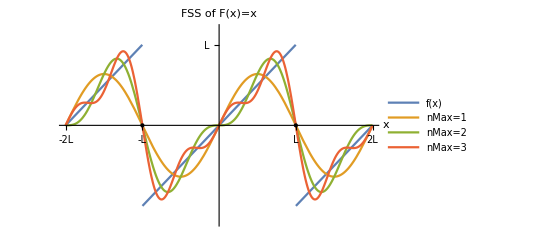

```mathematica
Plot[{fodd[x],PSSin[x,1],PSSin[x,2],PSSin[x,3]},{x,-2L,2L},PlotLabel->"FSS of F(x)=x", AxesLabel->{"x",""},PlotRange->{-1.2,1.2},BaseStyle->{FontSize->18},PlotStyle->Thick,PlotLegends->{"f(x)","nMax=1","nMax=2","nMax=3"},Ticks-> {{{-2,"-2L"},{-1,"-L"},{1,"L"},{2,"2L"}},{{1,"L"}}},Exclusions->{x==-L,x==L},Epilog->{PointSize[Large],Point[{{-L,0},{L,0}}]}]
```

#### Error of Fourier Sine Series to show ~10% error for 10 terms. The error at x=L will always be 100 % because the Fourier Sine Series converges to the average of the left and right limits at the jump discontinuity. The overshoot amplitude will remain relatively constant, but the width of the overshoot error will approach zero. This is called Gibbs phenomena.

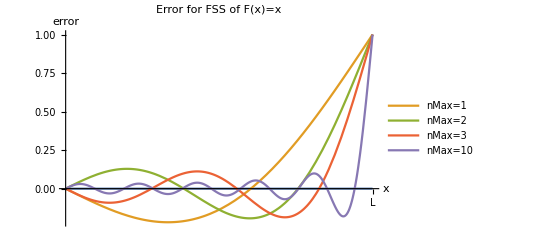

```mathematica
Plot[{0,fodd[x]-PSSin[x,1],fodd[x]-PSSin[x,2],fodd[x]-PSSin[x,3],fodd[x]-PSSin[x,10]},{x,0,L},PlotLabel->"Error for FSS of F(x)=x", AxesLabel->{"x","error"},PlotRange->All,BaseStyle->{FontSize->18},PlotStyle->Thick,PlotLegends->{"","nMax=1","nMax=2","nMax=3","nMax=10"},Ticks-> {{{1,"L"}},Automatic}]
```

```mathematica
Manipulate[Plot[{fodd[x],PSSin[x,nMax]},{x,-L,L},PlotRange->{-1.2,1.2},PlotLabel->Row[{"nMax = ",PaddedForm[nMax,{4,0}]}],AxesLabel->{"x","FCS"},BaseStyle->{FontSize->18},PlotStyle->Thick,Ticks-> {{{-1,"-L"},{1,"L"}},{{1,"L"}}}],{nMax,1,20,1}]
```

#### Compare the first few coefficient of the Fourier sine and cosine series. Note the 1/n versus the 1/n^2decay.

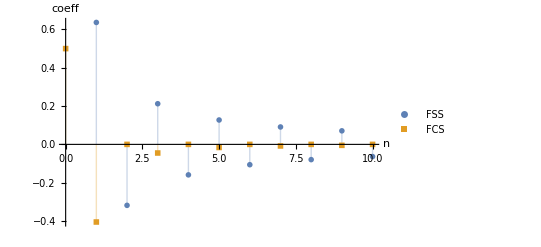

```mathematica
ListPlot[{FSScoefs,FCScoefs},Filling->Axis,BaseStyle->{FontSize->18},PlotMarkers->{Automatic,Medium},AxesLabel->{"n","coeff"},PlotLegends->{"FSS","FCS"},PlotRange->All]
```